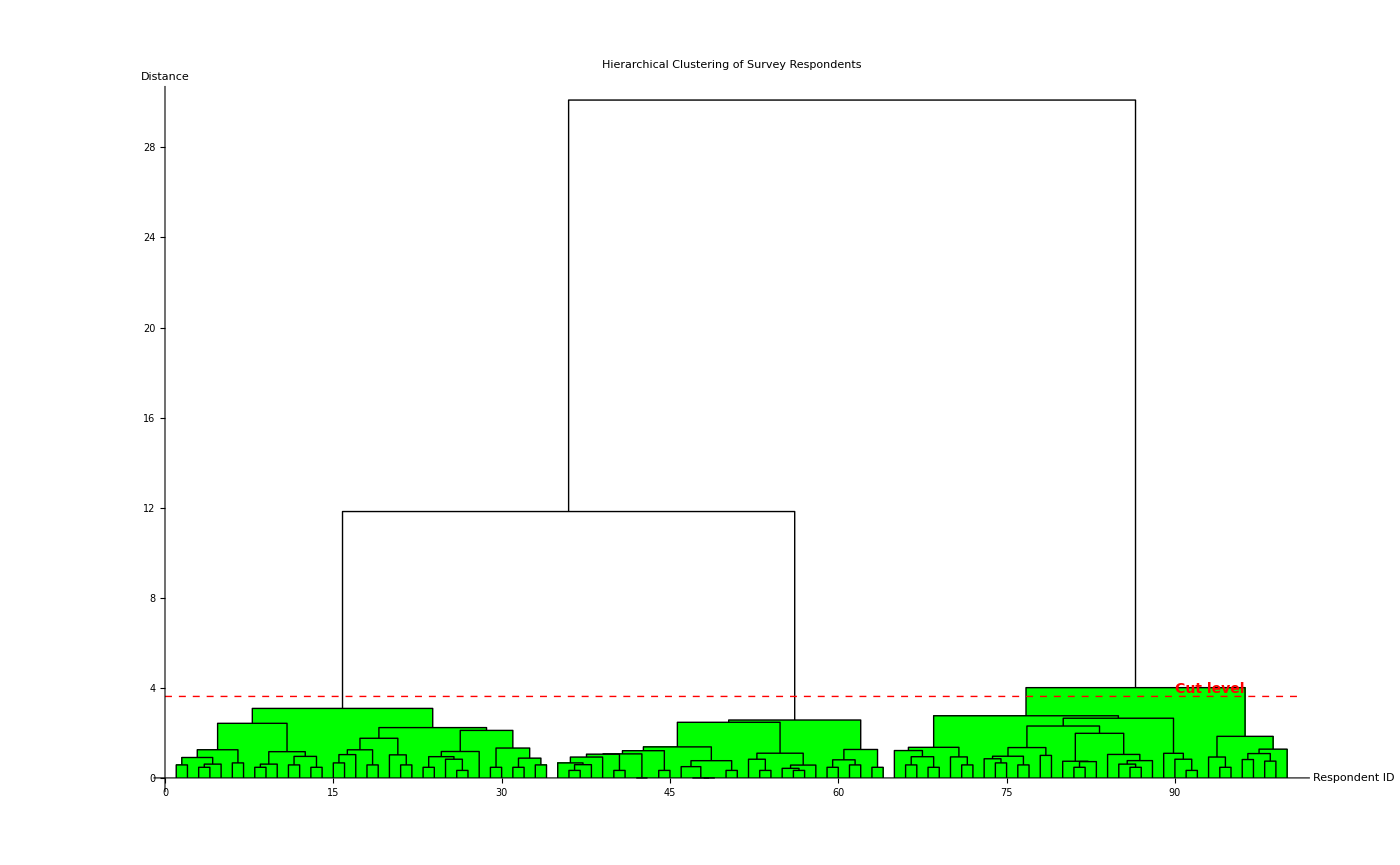

```mathematica
ClearAll["Global`*"];
Needs["HierarchicalClustering`"];

baseDir = DirectoryName[$InputFileName];
If[baseDir === "", baseDir = Directory[]];

data = Import["/Users/justy-dev/Documents/University/Semester-6/Модели и методы анализа проектных решений/lab1/survey_normed.csv", "CSV"];
header = First[data];
rows = Rest[data];
labels = ToString /@ rows[[All, 1]];
numericData = ToExpression /@ rows[[All, 2 ;; Length[header]]];
indexedData = Range[Length[numericData]];
cutHeight = 3.618278;

hierarcgdata = Agglomerate[
  indexedData,
  Linkage -> "Ward",
  DistanceFunction -> (EuclideanDistance[numericData[[#1]], numericData[[#2]]] &)
];

dendrogram = Show[
  DendrogramPlot[
    hierarcgdata,
    LeafLabels -> labels,
    HighlightLevel -> 3
  ],
  PlotLabel -> "Hierarchical Clustering of Survey Respondents",
  Axes -> True,
  AxesLabel -> {"Respondent ID", "Distance"},
  AxesOrigin -> {0, 0},
  ImageSize -> 1400,
  Epilog -> {
    {Red, Thick, Dashed, Line[{{0, cutHeight}, {Length[labels] + 1, cutHeight}}]},
    Inset[
      Style["Cut level", 14, Red, Bold],
      {Length[labels] * 0.9, cutHeight},
      {Left, Bottom}
    ]
  }
];

dendrogram
```